## Functions

```mathematica
gdg[a_,nx_,ny_,nz_,μ_]:=If[μ==1,
ConjugateTranspose[a[nx,ny,nz]].(a[nx+1,ny,nz]-a[nx-1,ny,nz]),
If[μ==2,
ConjugateTranspose[a[nx,ny,nz]].(a[nx,ny+1,nz]-a[nx,ny-1,nz]),
ConjugateTranspose[a[nx,ny,nz]].(a[nx,ny,nz+1]-a[nx,ny,nz-1])
]]
gdg[a_,nx_,ny_,nz_,μ_,sw_]:=If[μ==1,
ConjugateTranspose[a[nx+sw,ny,nz]].(a[nx+1+sw,ny,nz]-a[nx-1+sw,ny,nz]),
If[μ==2,
ConjugateTranspose[a[nx,ny+sw,nz]].(a[nx,ny+1+sw,nz]-a[nx,ny-1+sw,nz]),
ConjugateTranspose[a[nx,ny,nz+sw]].(a[nx,ny,nz+1+sw]-a[nx,ny,nz-1+sw])
]]
actiondensity[a_,nx_,ny_,nz_]:=Module[{d,l},
Do[
d[nx,ny,nz,μ]=gdg[a,nx,ny,nz,μ];
l[nx,ny,nz,μ]=d[nx,ny,nz,μ]-ConjugateTranspose[d[nx,ny,nz,μ]];
,{μ,1,3}
];
Re[(-1/16)Sum[Tr[l[nx,ny,nz,μ].l[nx,ny,nz,μ]],{μ,1,3}]]
]
action[a_,L_]:=Module[{s},
s=Sum[actiondensity[a,nx,ny,nz]
,{nx,0,L-1},{ny,0,L-1},{nz,0,L-1}];
Re[s/L^3]
]
W3[a_,L_]:=Module[{d,l},
Do[
d[nx,ny,nz,μ]=gdg[a,nx,ny,nz,μ];
l[nx,ny,nz,μ]=d[nx,ny,nz,μ]-ConjugateTranspose[d[nx,ny,nz,μ]];
,{nx,0,L-1},{ny,0,L-1},{nz,0,L-1}, {μ,1,3}
];
Re[3/(4^3*24Pi^2)*Sum[
Tr[l[nx,ny,nz,1].(l[nx,ny,nz,2].l[nx,ny,nz,3]-l[nx,ny,nz,3].l[nx,ny,nz,2])]
,{nx,0,L-1},{ny,0,L-1},{nz,0,L-1}]]
]
setWing[a_,L_]:=Module[{wmax=2},
Do[
a[-wing,ny,nz]=a[L-wing,ny,nz];
a[L-1+wing,ny,nz]=a[wing-1,ny,nz];
,{wing,1,wmax},{ny,0,L-1},{nz,0,L-1}];
Do[
a[nx,-wing,nz]=a[nx,L-wing,nz];
a[nx,L-1+wing,nz]=a[nx,wing-1,nz];
,{wing,1,wmax},{nx,-wmax,L-1+wmax},{nz,0,L-1}];
Do[
a[nx,ny,-wing]=a[nx,ny,L-wing];
a[nx,ny,L-1+wing]=a[nx,ny,wing-1];
,{wing,1,wmax},{nx,-wmax,L-1+wmax},{ny,-wmax,L-1+wmax}];
]
```

```mathematica
mapsuMatrix[m_,nx_,ny_,nz_,L_]:=Module[{unity,sigmax,sigmay,sigmaz,thetat,thetax,thetay,thetaz,norm,x,y,z},
unity={{1,0},{0,1}};
sigmax={{0,1},{1,0}};
sigmay={{0,-I},{I,0}};
sigmaz={{1,0},{0,-1}};

x=-Pi+2Pi nx/L;
y=-Pi+2Pi ny/L;
z=-Pi+2Pi nz/L;
thetat=m+Cos[x]-1+Cos[y]-1+Cos[z]-1;
thetax=Sin[x];thetay=Sin[y];thetaz=Sin[z];
norm=Sqrt[(thetat)^2+(thetax)^2+(thetay)^2+(thetaz)^2];

N[(thetat*unity+I*thetax*sigmax+I*thetay*sigmay+I*thetaz*sigmaz)/norm]
]
randomUnitaryMatrix[n_]:=Module[{A,Q,R,diagR},
A=RandomReal[{-1,1},{n,n}]+I RandomReal[{-1,1},{n,n}];
{Q,R}=QRDecomposition[A];
diagR=DiagonalMatrix[Exp[I Arg[Diagonal[R]]]];
Q.diagR
]
```

```mathematica
gfZ[a_,nx_,ny_,nz_]:=Module[{d,dp,dm,l},
d[nx,ny,nz,1]=gdg[a,nx,ny,nz,1];
d[nx,ny,nz,2]=gdg[a,nx,ny,nz,2];
d[nx,ny,nz,3]=gdg[a,nx,ny,nz,3];
dp[nx,ny,nz,1]=gdg[a,nx,ny,nz,1,1];
dp[nx,ny,nz,2]=gdg[a,nx,ny,nz,2,1];
dp[nx,ny,nz,3]=gdg[a,nx,ny,nz,3,1];
dm[nx,ny,nz,1]=gdg[a,nx,ny,nz,1,-1];
dm[nx,ny,nz,2]=gdg[a,nx,ny,nz,2,-1];
dm[nx,ny,nz,3]=gdg[a,nx,ny,nz,3,-1];

l[nx,ny,nz,1]=a[nx+1,ny,nz].d[nx,ny,nz,1].ConjugateTranspose[a[nx,ny,nz]]-a[nx-1,ny,nz].d[nx,ny,nz,1].ConjugateTranspose[a[nx,ny,nz]]+a[nx,ny,nz].dp[nx,ny,nz,1].ConjugateTranspose[a[nx+1,ny,nz]]-a[nx,ny,nz].dm[nx,ny,nz,1].ConjugateTranspose[a[nx-1,ny,nz]]+a[nx+2,ny,nz].ConjugateTranspose[a[nx,ny,nz]]+a[nx-2,ny,nz].ConjugateTranspose[a[nx,ny,nz]];

l[nx,ny,nz,2]=a[nx,ny+1,nz].d[nx,ny,nz,2].ConjugateTranspose[a[nx,ny,nz]]-a[nx,ny-1,nz].d[nx,ny,nz,2].ConjugateTranspose[a[nx,ny,nz]]+a[nx,ny,nz].dp[nx,ny,nz,2].ConjugateTranspose[a[nx,ny+1,nz]]-a[nx,ny,nz].dm[nx,ny,nz,2].ConjugateTranspose[a[nx,ny-1,nz]]+a[nx,ny+2,nz].ConjugateTranspose[a[nx,ny,nz]]+a[nx,ny-2,nz].ConjugateTranspose[a[nx,ny,nz]];

l[nx,ny,nz,3]=a[nx,ny,nz+1].d[nx,ny,nz,3].ConjugateTranspose[a[nx,ny,nz]]-a[nx,ny,nz-1].d[nx,ny,nz,3].ConjugateTranspose[a[nx,ny,nz]]+a[nx,ny,nz].dp[nx,ny,nz,3].ConjugateTranspose[a[nx,ny,nz+1]]-a[nx,ny,nz].dm[nx,ny,nz,3].ConjugateTranspose[a[nx,ny,nz-1]]+a[nx,ny+2,nz].ConjugateTranspose[a[nx,ny,nz]]+a[nx,ny-2,nz].ConjugateTranspose[a[nx,ny,nz]];

(1/16)Sum[l[nx,ny,nz,μ]-ConjugateTranspose[l[nx,ny,nz,μ]],{μ,1,3}]
]
gfZsu[a_,nx_,ny_,nz_]:=Module[{nc,z},
nc=Length[a[nx,ny,nz]];
z[nx,ny,nz]=gfZ[a,nx,ny,nz];
z[nx,ny,nz] - (1/nc) Tr[z[nx,ny,nz]]IdentityMatrix[nc]
]
```

```mathematica
flowW3[a_,Δt_,tmax_,L_,Z_]:=Module[{tblW,tblS,gflow,z0,z1,z2,w0,w1,w2,j},
tblW=Table[{t,0},{t,0,tmax,Δt}];
tblS=Table[{t,0},{t,0,tmax,Δt}];
j=1;
Do[
gflow[nx,ny,nz]=a[nx,ny,nz],{nx,-2,L+1},{ny,-2,L+1},{nz,-2,L+1}
];
tblW[[j,2]]=W3[gflow,L];
tblS[[j,2]]=action[gflow,L];
Monitor[Do[
Do[
w0[nx,ny,nz]=gflow[nx,ny,nz],{nx,-2,L+1},{ny,-2,L+1},{nz,-2,L+1}
];
Do[
z0[nx,ny,nz]=Δt*Z[w0,nx,ny,nz],{nx,0,L-1},{ny,0,L-1},{nz,0,L-1}
];
setWing[z0,L];
Do[
w1[nx,ny,nz]=MatrixExp[(1/4)z0[nx,ny,nz]].w0[nx,ny,nz]
,{nx,-2,L+1},{ny,-2,L+1},{nz,-2,L+1}
];
Do[
z1[nx,ny,nz]=Δt*Z[w1,nx,ny,nz],{nx,0,L-1},{ny,0,L-1},{nz,0,L-1}
];
setWing[z1,L];
Do[
w2[nx,ny,nz]=MatrixExp[(8/9)z1[nx,ny,nz]-(17/36)z0[nx,ny,nz]].w1[nx,ny,nz]
,{nx,-2,L+1},{ny,-2,L+1},{nz,-2,L+1}
];
Do[
z2[nx,ny,nz]=Δt*Z[w2,nx,ny,nz],{nx,0,L-1},{ny,0,L-1},{nz,0,L-1}
];
setWing[z2,L];
j++;
Do[
gflow[nx,ny,nz]=MatrixExp[(3/4)z2[nx,ny,nz]-(8/9)z1[nx,ny,nz]+(17/36)z0[nx,ny,nz]].w2[nx,ny,nz]
,{nx,-2,L+1},{ny,-2,L+1},{nz,-2,L+1}
];
tblW[[j,2]]=W3[gflow,L];
tblS[[j,2]]=action[gflow,L];
,{t,Δt,tmax,Δt}
],t];
{tblW,tblS}
]
```

## T^3->SU(2)

```mathematica
L=30;
m=3;
Do[
g[nx,ny,nz]=mapsuMatrix[m,nx,ny,nz,L];
,{nx,0,L-1},{ny,0,L-1},{nz,0,L-1}
];
setWing[g,L]
```

```mathematica
W3[g,L]
action[g,L]
```

-1.93661

0.100885

```mathematica
(* tmax=40 for L=10; tmax=80 for L=20; tmax=160 for L=30 *)
```

```mathematica
δt=0.1;
tm=160;
tbl=flowW3[g,δt,tm,L,gfZsu];
```

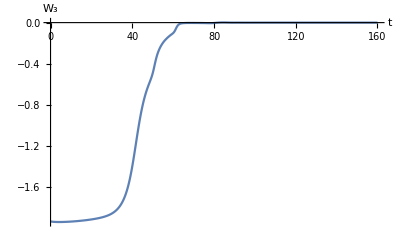

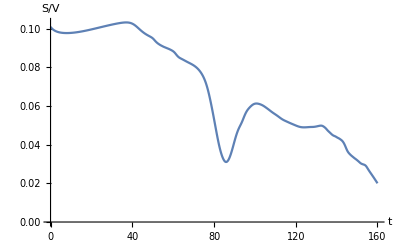

```mathematica
ListPlot[tbl[[1]],Joined->True,PlotRange->Full,AxesLabel->{Style[t,16],Style[Subscript[W, 3],16]}]
ListPlot[tbl[[2]],Joined->True,PlotRange->Full,AxesLabel->{Style[t,16],Style[S/V,16]}]
```

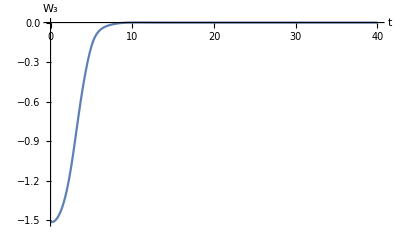
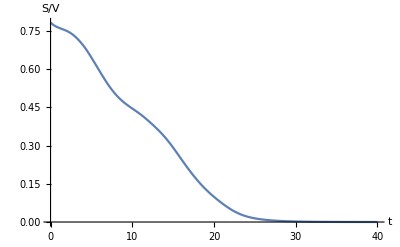
```mathematica
(* L=10; m=3; δt=0.1, tmax=40 *)
{-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-}

## Random

```mathematica
L=10;
Do[
g[nx,ny,nz]=randomUnitaryMatrix[2];
,{nx,0,L-1},{ny,0,L-1},{nz,0,L-1}
];
setWing[g,L]
W3[g,L]
action[g,L]
```

0.124632

1.49458

```mathematica
δt=0.1;
tm=40;
tbl=flowW3[g,δt,tm,L,gfZ];
```

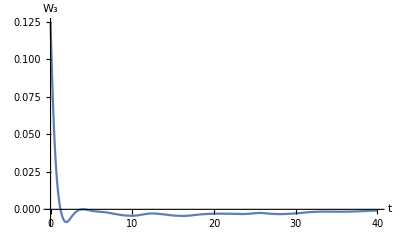

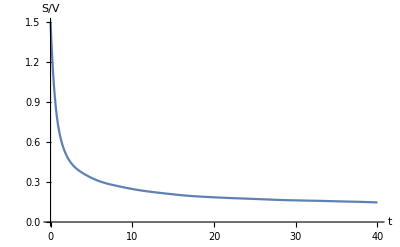

```mathematica
ListPlot[tbl[[1]],Joined->True,PlotRange->Full,AxesLabel->{Style[t,16],Style[Subscript[W, 3],16]}]
ListPlot[tbl[[2]],Joined->True,PlotRange->Full,AxesLabel->{Style[t,16],Style[S/V,16]}]
```